### Start choosing the example:

```mathematica
t="New Braess";
alpha = 1;
beta = 0;
A = 0;
g[x]
```

Log[x]

### DataToEquations and the Braess phenomenon (split)

```mathematica
Data=DataG[t];
Data
```

<|Vertices List→{1,2,3,4,5,6},Adjacency Matrix→{{0,1,0,1,0,0},{0,0,1,0,0,0},{0,0,0,0,0,1},{0,0,0,0,1,0},{0,0,0,0,0,1},{0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,4000}},Exit Vertices and Terminal Costs→{{6,0}},Switching Costs→{{1,2,3,45},{3,2,1,45},{4,5,6,45},{6,5,4,45}},a→Function[{j,edge},Which[edge===3->6||edge===1->4,j/100,True,0]]|>

DataToEquations: Triangle inequalities for switching costs: {True,True,True,True}
DataToEquations: Reduced: True

DataToEquations: The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.132243 seconds to reduce the critical congestion case with NewReduce!
The system is j112==2000&&j120==0&&jt139==0&&u147==45&&u148==0&&u150==65

DataToEquations: Critical congestion solved.

{0.21799,Null}

jvars

<|{2,1->2}→2000,{4,1->4}→2000,{3,2->3}→2000,{6,3->6}→2000,{5,4->5}→2000,{6,5->6}→2000,{ex106,6->ex106}→4000,{1,en105->1}→4000,{1,1->2}→0,{1,1->4}→0,{2,2->3}→0,{3,3->6}→0,{4,4->5}→0,{5,5->6}→0,{6,6->ex106}→0,{en105,en105->1}→0|>

uvars

<|{1,1->2}→65,{1,1->4}→65,{2,2->3}→20,{3,3->6}→20,{4,4->5}→45,{5,5->6}→0,{6,6->ex106}→0,{en105,en105->1}→65,{2,1->2}→65,{4,1->4}→45,{3,2->3}→20,{6,3->6}→0,{5,4->5}→45,{6,5->6}→0,{ex106,6->ex106}→0,{1,en105->1}→65|>

jtvars

<|{1,1->2,1->4}→0,{1,1->2,en105->1}→0,{1,1->4,1->2}→0,{1,1->4,en105->1}→0,{1,en105->1,1->2}→2000,{1,en105->1,1->4}→2000,{2,1->2,2->3}→2000,{2,2->3,1->2}→0,{3,2->3,3->6}→2000,{3,3->6,2->3}→0,{4,1->4,4->5}→2000,{4,4->5,1->4}→0,{5,4->5,5->6}→2000,{5,5->6,4->5}→0,{6,3->6,5->6}→0,{6,3->6,6->ex106}→2000,{6,5->6,3->6}→0,{6,5->6,6->ex106}→2000,{6,6->ex106,3->6}→0,{6,6->ex106,5->6}→0|>

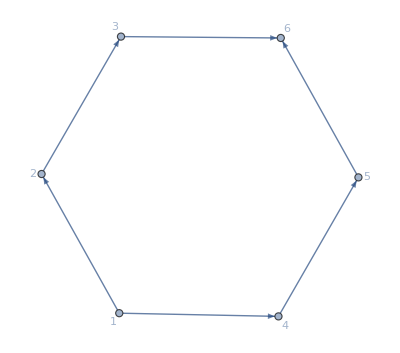

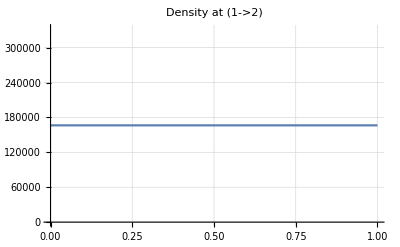
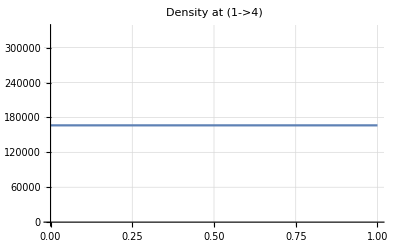
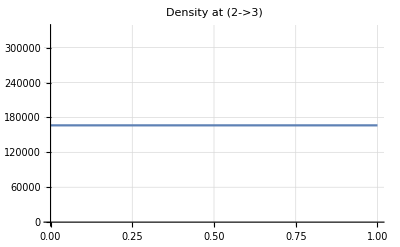
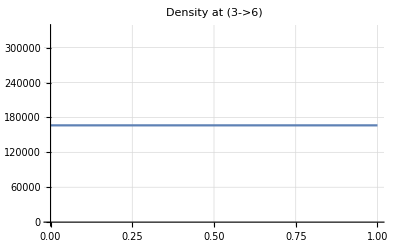
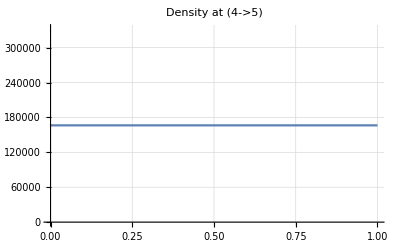
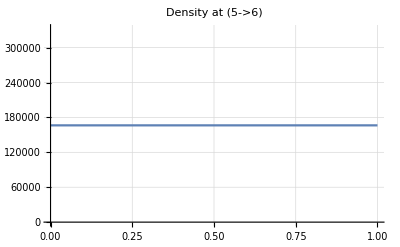

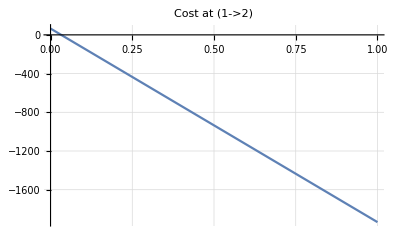

```mathematica
MFGEquations=DataToEquations[Data];//Timing
Print["jvars"];
MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]
Print["uvars"];
MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]
Print["jtvars"];
MFGEquations["jtvars"]/.MFGEquations["criticalreduced1"][[2]]
(*Don't forget to change the Range!*)
MFGEquations["BG"]
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"Density at " #,(*PlotRange->{-0.1,2.4},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"Cost at " #(*,PlotRange->{1-0.1,4.7}*),GridLines->Automatic]&/@MFGEquations["BEL"]
```

### Start choosing the example:

```mathematica
t="New Braess";
alpha =1;
beta = 0;
A = 0;
g[x]
```

Log[x]

### DataToEquations and Braess phenomenon (congest)

```mathematica
Data=DataG[t];
Data["Adjacency Matrix"]={{0,1,0,1,0,0},{0,0,1,0,0,0},{0,0,0,1,0,1},{0,0,0,0,1,0},{0,0,0,0,0,1},{0,0,0,0,0,0}};
Data
```

<|Vertices List→{1,2,3,4,5,6},Adjacency Matrix→{{0,1,0,1,0,0},{0,0,1,0,0,0},{0,0,0,1,0,1},{0,0,0,0,1,0},{0,0,0,0,0,1},{0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,4000}},Exit Vertices and Terminal Costs→{{6,0}},Switching Costs→{{1,2,3,45},{3,2,1,45},{4,5,6,45},{6,5,4,45}},a→Function[{j,edge},Which[edge===3->6||edge===1->4,j/100,True,0]]|>

DataToEquations: Triangle inequalities for switching costs: {True,True,True,True}
DataToEquations: Reduced: True

DataToEquations: The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.841066 seconds to reduce the critical congestion case with NewReduce!
The system is j186==4000&&j187==0&&j191==0&&j200==0&&jt212==0&&jt215==0&&jt218==0&&jt221==0&&jt227==0&&u237==0&&u239==80

DataToEquations: Critical congestion solved.

{0.999574,Null}

jvars

<|{2,1->2}→0,{4,1->4}→4000,{3,2->3}→0,{4,3->4}→0,{6,3->6}→4000,{5,4->5}→0,{6,5->6}→0,{ex184,6->ex184}→4000,{1,en183->1}→4000,{1,1->2}→0,{1,1->4}→0,{2,2->3}→0,{3,3->4}→4000,{3,3->6}→0,{4,4->5}→0,{5,5->6}→0,{6,6->ex184}→0,{en183,en183->1}→0|>

uvars

<|{1,1->2}→80,{1,1->4}→80,{2,2->3}→40,{3,3->4}→40,{3,3->6}→40,{4,4->5}→40,{5,5->6}→0,{6,6->ex184}→0,{en183,en183->1}→80,{2,1->2}→80,{4,1->4}→40,{3,2->3}→40,{4,3->4}→40,{6,3->6}→0,{5,4->5}→40,{6,5->6}→0,{ex184,6->ex184}→0,{1,en183->1}→80|>

jtvars

<|{1,1->2,1->4}→0,{1,1->2,en183->1}→0,{1,1->4,1->2}→0,{1,1->4,en183->1}→0,{1,en183->1,1->2}→0,{1,en183->1,1->4}→4000,{2,1->2,2->3}→0,{2,2->3,1->2}→0,{3,2->3,3->4}→0,{3,2->3,3->6}→0,{3,3->4,2->3}→0,{3,3->4,3->6}→4000,{3,3->6,2->3}→0,{3,3->6,3->4}→0,{4,1->4,3->4}→4000,{4,1->4,4->5}→0,{4,3->4,1->4}→0,{4,3->4,4->5}→0,{4,4->5,1->4}→0,{4,4->5,3->4}→0,{5,4->5,5->6}→0,{5,5->6,4->5}→0,{6,3->6,5->6}→0,{6,3->6,6->ex184}→4000,{6,5->6,3->6}→0,{6,5->6,6->ex184}→0,{6,6->ex184,3->6}→0,{6,6->ex184,5->6}→0|>

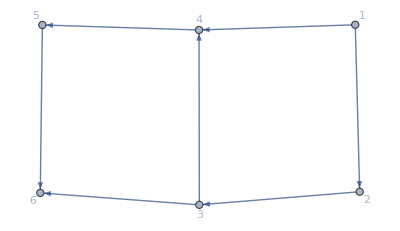

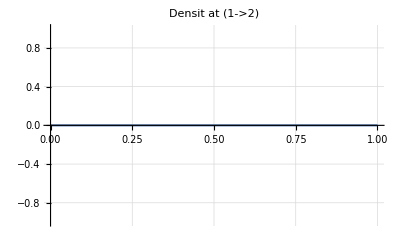
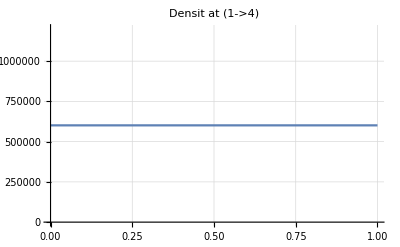
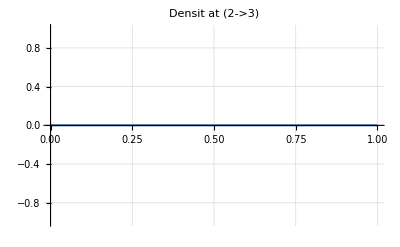
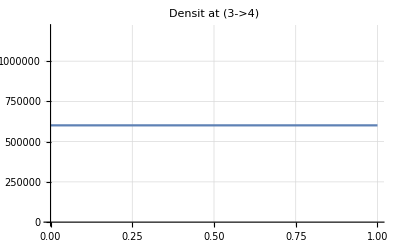
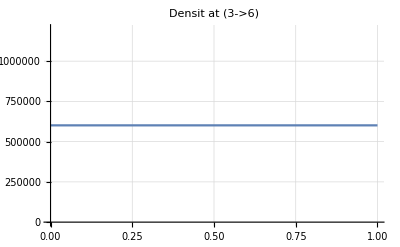
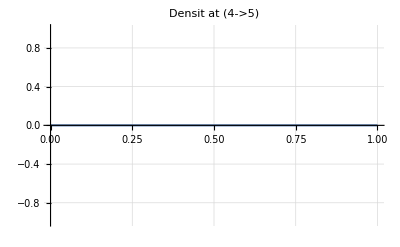
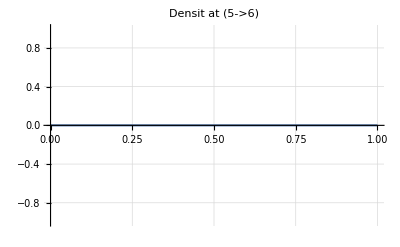

```mathematica
MFGEquations=DataToEquations[Data];//Timing
Print["jvars"];
MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]
Print["uvars"];
MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]
Print["jtvars"];
MFGEquations["jtvars"]/.MFGEquations["criticalreduced1"][[2]]
(*Don't forget to change the Range!*)
MFGEquations["BG"]
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"Densit at " #,(*PlotRange->{-0.1,2.4},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"Cost at " #(*,PlotRange->{1-0.1,4.7}*),GridLines->Automatic]&/@MFGEquations["BEL"]
```